# Comparison of DMS immune escape to MLR growth advantage

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/ncov-escape/escape-mlr-comparison

## Colors

```mathematica
toHexString[n_Integer]:=StringJoin[ToString/@(IntegerDigits[n,16]/.Thread[Range[10,15]->CharacterRange["A","F"]])]
```

```mathematica
rgbColorToHex[rgbColor_]:="#"<>StringJoin[Map[toHexString[Round[#*255]]&,Level[rgbColor,1]]]
```

```mathematica
start[n_]:=0.07;
```

```mathematica
stop[n_]:=0.99;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
colors=Append[makeColors[6],Gray]
```

{RGBColor[0.30382016, 0.13051672, 0.67703096],RGBColor[0.26866900800000004, 0.492994304, 0.7985057680000001],RGBColor[0.4305106, 0.702073568, 0.5395238880000001],RGBColor[0.7003634240000002, 0.742645096, 0.30201920799999993],RGBColor[0.897113792, 0.5919722799999999, 0.218624288],RGBColor[0.86067868, 0.15704232000000004, 0.13666448],GrayLevel[0.5]}

```mathematica
legendPanel=SwatchLegend[colors,{"BA.2","BA.4","BA.5","BA.2.75","BQ.1","XBB","other"},LegendMarkerSize->11,LegendLayout->{"Column",1},Spacings->{0,1}]
```

```mathematica
colorRamp[t_]:=Blend[{GrayLevel[0.99],Lighter[ColorData["Rainbow"][0.75],0.4],Lighter[ColorData["Rainbow"][0.75],0.05],RGBColor[0.5807,0.6182,0.4944],Darker[ColorData["Rainbow"][0.3],0.05],Darker[ColorData["Rainbow"][0.3],0.4],GrayLevel[0.05]},t]
```

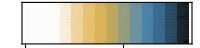

```mathematica
gaPanel=Rotate[DensityPlot[(x-0.5)/2,{x,0,2.5},{y,0,1},ColorFunction->colorRamp,ColorFunctionScaling->False,AspectRatio->0.1,PlotRangePadding->0,FrameTicks->{{None,None},{Automatic,None}}, ImageSize->200],Pi/2]
```

## Immune escape

```mathematica
escape=Import["../escape-score/escape_scores.tsv","TSV"];
```

```mathematica
escapeHeader=escape[[1]]
```

{seqName,clade,Nextclade_pango,partiallyAliased,immune_escape,ace2_binding}

```mathematica
escapeHeaderRules=MapIndexed[#1->#2[[1]]&,escapeHeader]
```

{seqName→1,clade→2,Nextclade_pango→3,partiallyAliased→4,immune_escape→5,ace2_binding→6}

```mathematica
escape=Drop[escape,1];
```

```mathematica
escape=DeleteCases[escape,x_/;x[[2]]=="outgroup"];
```

```mathematica
Length[escape]
```

496

```mathematica
TableForm[escape,TableHeadings->{None,escapeHeader}]
```

seqName | clade | Nextclade_pango | partiallyAliased | immune_escape | ace2_binding
BA.2 | 21L (Omicron) | BA.2 | BA.2 | 0 | 0
XBA | recombinant | XBA | XBA | 0.315502 | 0.20216
XAV | recombinant | XAV | XAV | 0.386325 | 0.55831
XAN | recombinant | XAN | XAN | 0.386325 | 0.55831
XBD | recombinant | XBD | XBD | 0.633879 | 0.4677
XAJ | recombinant | XAJ | XAJ | 0.386325 | 0.35483
XAZ | recombinant | XAZ | XAZ | 0.386325 | 0.55831
XAS | recombinant | XAS | XAS | 0.386325 | 0.55831
XAY | recombinant | XAY | XAY | 0.528346 | 0.61445
XAY.1 | recombinant | XAY.1 | XAY.1 | 0.528346 | 0.61445
XAY.2 | recombinant | XAY.2 | XAY.2 | 0.528346 | 0.61445
XBC | recombinant | XBC | XBC | 0.326298 | 0.68716
XBC.2 | recombinant | XBC.2 | XBC.2 | 0.326298 | 0.68716
XBC.1 | recombinant | XBC.1 | XBC.1 | 0.528346 | 0.79272
XBB | 22F (Omicron) | XBB | XBB | 0.907001 | 0.40687
XBB.5 | 22F (Omicron) | XBB.5 | XBB.5 | 0.907001 | 0.40687
XBB.2 | 22F (Omicron) | XBB.2 | XBB.2 | 0.907001 | 0.40687
XBB.4 | 22F (Omicron) | XBB.4 | XBB.4 | 0.979915 | 0.30641
XBB.3 | 22F (Omicron) | XBB.3 | XBB.3 | 0.907001 | 0.40687
XBB.3.1 | 22F (Omicron) | XBB.3.1 | XBB.3.1 | 0.907001 | 0.40687
XBB.1 | 22F (Omicron) | XBB.1 | XBB.1 | 0.907001 | 0.40687
XBB.1.1 | 22F (Omicron) | XBB.1.1 | XBB.1.1 | 0.907001 | 0.40687
XBB.1.2 | 22F (Omicron) | XBB.1.2 | XBB.1.2 | 0.907001 | 0.40687
XBB.1.3 | 22F (Omicron) | XBB.1.3 | XBB.1.3 | 0.983269 | 0.49564
BA.2.16 | 21L (Omicron) | BA.2.16 | BA.2.16 | -0.000089996 | 0
BA.2.15 | 21L (Omicron) | BA.2.15 | BA.2.15 | -0.000089996 | 0
BA.2.19 | 21L (Omicron) | BA.2.19 | BA.2.19 | -0.000089996 | 0
BA.2.1 | 21L (Omicron) | BA.2.1 | BA.2.1 | -0.000089996 | 0
BA.2.11 | 21L (Omicron) | BA.2.11 | BA.2.11 | 0.171804 | -0.04096
BA.2.18 | 21L (Omicron) | BA.2.18 | BA.2.18 | 0.047316 | 0.23107
BA.2.20 | 21L (Omicron) | BA.2.20 | BA.2.20 | -0.000089996 | 0
BA.2.24 | 21L (Omicron) | BA.2.24 | BA.2.24 | 0.0131085 | -0.03172
BA.2.26 | 21L (Omicron) | BA.2.26 | BA.2.26 | -0.000089996 | 0
BA.2.27 | 21L (Omicron) | BA.2.27 | BA.2.27 | -0.000089996 | 0
BA.2.28 | 21L (Omicron) | BA.2.28 | BA.2.28 | -0.000089996 | 0
BA.2.29 | 21L (Omicron) | BA.2.29 | BA.2.29 | -0.000089996 | 0
BA.2.30 | 21L (Omicron) | BA.2.30 | BA.2.30 | -0.000089996 | 0
BA.2.32 | 21L (Omicron) | BA.2.32 | BA.2.32 | -0.000089996 | 0
BA.2.4 | 21L (Omicron) | BA.2.4 | BA.2.4 | -0.000089996 | 0
BA.2.39 | 21L (Omicron) | BA.2.39 | BA.2.39 | -0.000089996 | 0
BA.2.41 | 21L (Omicron) | BA.2.41 | BA.2.41 | -0.000089996 | 0
BA.2.43 | 21L (Omicron) | BA.2.43 | BA.2.43 | 0.017546 | 0.11285
BA.2.42 | 21L (Omicron) | BA.2.42 | BA.2.42 | -0.000089996 | 0
BA.2.46 | 21L (Omicron) | BA.2.46 | BA.2.46 | -0.000089996 | 0
BA.2.48 | 21L (Omicron) | BA.2.48 | BA.2.48 | -0.000089996 | 0
BA.2.5 | 21L (Omicron) | BA.2.5 | BA.2.5 | -0.000089996 | 0
BA.2.55 | 21L (Omicron) | BA.2.55 | BA.2.55 | -0.000089996 | 0
BA.2.54 | 21L (Omicron) | BA.2.54 | BA.2.54 | -0.000089996 | 0
BA.2.58 | 21L (Omicron) | BA.2.58 | BA.2.58 | -0.000089996 | 0
BA.2.59 | 21L (Omicron) | BA.2.59 | BA.2.59 | -0.000089996 | 0
BA.2.60 | 21L (Omicron) | BA.2.60 | BA.2.60 | -0.000089996 | 0
BA.2.62 | 21L (Omicron) | BA.2.62 | BA.2.62 | -0.000089996 | 0
BA.2.61 | 21L (Omicron) | BA.2.61 | BA.2.61 | -0.000089996 | 0
BA.2.63 | 21L (Omicron) | BA.2.63 | BA.2.63 | -0.000089996 | 0
BA.2.65 | 21L (Omicron) | BA.2.65 | BA.2.65 | -0.000089996 | 0
BA.2.64 | 21L (Omicron) | BA.2.64 | BA.2.64 | -0.000089996 | 0
BA.2.70 | 21L (Omicron) | BA.2.70 | BA.2.70 | -0.000089996 | 0
BA.2.77 | 21L (Omicron) | BA.2.77 | BA.2.77 | 0.380024 | 0.92132
BA.2.8 | 21L (Omicron) | BA.2.8 | BA.2.8 | -0.000089996 | 0
BA.2.82 | 21L (Omicron) | BA.2.82 | BA.2.82 | 0.215487 | 0.11142
BA.2.83 | 21L (Omicron) | BA.2.83 | BA.2.83 | 0.179303 | 1.12534
BA.2.85 | 21L (Omicron) | BA.2.85 | BA.2.85 | -0.000089996 | 0
BA.2.2.1 | 21L (Omicron) | BA.2.2.1 | BA.2.2.1 | -0.000089996 | 0
BA.2.2 | 21L (Omicron) | BA.2.2 | BA.2.2 | -0.000089996 | 0
BA.2.23.1 | 21L (Omicron) | BA.2.23.1 | BA.2.23.1 | -0.000089996 | 0
BA.2.23 | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
BA.2.31 | 21L (Omicron) | BA.2.31 | BA.2.31 | -0.000089996 | 0
BA.2.31.1 | 21L (Omicron) | BA.2.31.1 | BA.2.31.1 | -0.000089996 | 0
BA.2.33 | 21L (Omicron) | BA.2.33 | BA.2.33 | -0.000089996 | 0
BA.2.35 | 21L (Omicron) | BA.2.35 | BA.2.35 | 0.171804 | -0.04096
BA.2.40.1 | 21L (Omicron) | BA.2.40.1 | BA.2.40.1 | 0.047316 | 0.23107
BA.2.40 | 21L (Omicron) | BA.2.40 | BA.2.40 | -0.000089996 | 0
BA.2.49 | 21L (Omicron) | BA.2.49 | BA.2.49 | -0.000089996 | 0
BA.2.50 | 21L (Omicron) | BA.2.50 | BA.2.50 | -0.000089996 | 0
BA.2.56 | 21L (Omicron) | BA.2.56 | BA.2.56 | 0.171804 | 0.10556
BA.2.56.1 | 21L (Omicron) | BA.2.56.1 | BA.2.56.1 | 0.171804 | 0.10556
BA.2.10 | 21L (Omicron) | BA.2.10 | BA.2.10 | -0.000089996 | 0
BA.2.10.2 | 21L (Omicron) | BA.2.10.2 | BA.2.10.2 | -0.000089996 | 0
BA.2.10.3 | 21L (Omicron) | BA.2.10.3 | BA.2.10.3 | -0.000089996 | 0
BA.2.10.4 | 21L (Omicron) | BA.2.10.4 | BA.2.10.4 | 0.362464 | 0.73328
BA.2.10.1 | 21L (Omicron) | BA.2.10.1 | BA.2.10.1 | -0.000089996 | 0
BJ.1 | 21L (Omicron) | BJ.1 | BA.2.10.1.1 | 0.571427 | 0.09519
BA.2.14 | 21L (Omicron) | BA.2.14 | BA.2.14 | -0.000089996 | 0
BA.2.22 | 21L (Omicron) | BA.2.22 | BA.2.22 | -0.000089996 | 0
BA.2.34 | 21L (Omicron) | BA.2.34 | BA.2.34 | -0.000089996 | 0
BA.2.36 | 21L (Omicron) | BA.2.36 | BA.2.36 | -0.000089996 | 0
BA.2.47 | 21L (Omicron) | BA.2.47 | BA.2.47 | -0.000089996 | 0
BA.2.45 | 21L (Omicron) | BA.2.45 | BA.2.45 | 0.0675245 | -0.30756
BA.2.51 | 21L (Omicron) | BA.2.51 | BA.2.51 | -0.000089996 | 0
BA.2.53 | 21L (Omicron) | BA.2.53 | BA.2.53 | 0.0675245 | -0.33553
BA.2.52 | 21L (Omicron) | BA.2.52 | BA.2.52 | -0.000089996 | 0
BA.2.6 | 21L (Omicron) | BA.2.6 | BA.2.6 | -0.000089996 | 0
BA.2.7 | 21L (Omicron) | BA.2.7 | BA.2.7 | -0.000089996 | 0
BA.2.69 | 21L (Omicron) | BA.2.69 | BA.2.69 | -0.000089996 | 0
BA.2.71 | 21L (Omicron) | BA.2.71 | BA.2.71 | -0.000089996 | 0
BA.2.72 | 21L (Omicron) | BA.2.72 | BA.2.72 | -0.000089996 | 0
BA.2.81 | 21L (Omicron) | BA.2.81 | BA.2.81 | 0.171804 | 0.10556
BA.2.80 | 21L (Omicron) | BA.2.80 | BA.2.80 | 0.37993 | 0.10838
BA.2.25 | 21L (Omicron) | BA.2.25 | BA.2.25 | -0.000089996 | 0
BA.2.25.1 | 21L (Omicron) | BA.2.25.1 | BA.2.25.1 | -0.000089996 | 0
BA.2.44 | 21L (Omicron) | BA.2.44 | BA.2.44 | 0.017546 | 0.11285
BA.2.13 | 21L (Omicron) | BA.2.13 | BA.2.13 | 0.171804 | 0.10556
BA.2.13.1 | 21L (Omicron) | BA.2.13.1 | BA.2.13.1 | 0.171804 | 0.10556
BA.2.9 | 21L (Omicron) | BA.2.9 | BA.2.9 | -0.000089996 | 0
BA.2.9.2 | 21L (Omicron) | BA.2.9.2 | BA.2.9.2 | -0.000089996 | 0
BA.2.9.3 | 21L (Omicron) | BA.2.9.3 | BA.2.9.3 | -0.000089996 | 0
BA.2.9.1 | 21L (Omicron) | BA.2.9.1 | BA.2.9.1 | 0.171804 | 0.10556
BA.2.9.4 | 21L (Omicron) | BA.2.9.4 | BA.2.9.4 | 0.215487 | 0.11142
BA.2.9.5 | 21L (Omicron) | BA.2.9.5 | BA.2.9.5 | -0.000089996 | 0
BA.2.9.6 | 21L (Omicron) | BA.2.9.6 | BA.2.9.6 | 0.171804 | 0.10556
BA.2.3.10 | 21L (Omicron) | BA.2.3.10 | BA.2.3.10 | -0.000089996 | 0
BA.2.3.1 | 21L (Omicron) | BA.2.3.1 | BA.2.3.1 | -0.000089996 | 0
BA.2.3 | 21L (Omicron) | BA.2.3 | BA.2.3 | -0.000089996 | 0
BA.2.3.12 | 21L (Omicron) | BA.2.3.12 | BA.2.3.12 | -0.000089996 | 0
BA.2.3.13 | 21L (Omicron) | BA.2.3.13 | BA.2.3.13 | -0.000089996 | 0
BA.2.3.11 | 21L (Omicron) | BA.2.3.11 | BA.2.3.11 | -0.000089996 | 0
BA.2.3.14 | 21L (Omicron) | BA.2.3.14 | BA.2.3.14 | -0.000089996 | 0
BA.2.3.15 | 21L (Omicron) | BA.2.3.15 | BA.2.3.15 | -0.000089996 | 0
BA.2.3.17 | 21L (Omicron) | BA.2.3.17 | BA.2.3.17 | -0.000089996 | 0
BA.2.3.18 | 21L (Omicron) | BA.2.3.18 | BA.2.3.18 | -0.000089996 | 0
BA.2.3.19 | 21L (Omicron) | BA.2.3.19 | BA.2.3.19 | 0.047316 | 0.23107
BA.2.3.21 | 21L (Omicron) | BA.2.3.21 | BA.2.3.21 | 0.0197094 | 1.06758
BA.2.3.4 | 21L (Omicron) | BA.2.3.4 | BA.2.3.4 | -0.000089996 | 0
BA.2.3.5 | 21L (Omicron) | BA.2.3.5 | BA.2.3.5 | -0.000089996 | 0
BA.2.3.7 | 21L (Omicron) | BA.2.3.7 | BA.2.3.7 | -0.000089996 | 0
BA.2.3.6 | 21L (Omicron) | BA.2.3.6 | BA.2.3.6 | -0.000089996 | 0
BA.2.3.8 | 21L (Omicron) | BA.2.3.8 | BA.2.3.8 | -0.000089996 | 0
BA.2.3.9 | 21L (Omicron) | BA.2.3.9 | BA.2.3.9 | -0.000089996 | 0
BA.2.3.16 | 21L (Omicron) | BA.2.3.16 | BA.2.3.16 | -0.000089996 | 0
BP.1 | 21L (Omicron) | BP.1 | BA.2.3.16.1 | 0.366094 | 0.94569
BA.2.3.2 | 21L (Omicron) | BA.2.3.2 | BA.2.3.2 | -0.000089996 | 0
BS.1 | 21L (Omicron) | BS.1 | BA.2.3.2.1 | 0.467909 | 0.66194
BS.1.1 | 21L (Omicron) | BS.1.1 | BA.2.3.2.1.1 | 0.636953 | 0.6589
BA.2.3.20 | 21L (Omicron) | BA.2.3.20 | BA.2.3.20 | 0.592504 | 1.06344
CM.6 | 21L (Omicron) | CM.6 | BA.2.3.20.6 | 0.592504 | 1.06344
CM.1 | 21L (Omicron) | CM.1 | BA.2.3.20.1 | 0.592504 | 1.06344
CM.4 | 21L (Omicron) | CM.4 | BA.2.3.20.4 | 0.592504 | 1.06344
CM.5 | 21L (Omicron) | CM.5 | BA.2.3.20.5 | 0.592504 | 1.06344
CM.2 | 21L (Omicron) | CM.2 | BA.2.3.20.2 | 0.592504 | 1.06344
CM.3 | 21L (Omicron) | CM.3 | BA.2.3.20.3 | 0.656153 | 0.29833
BA.2.17 | 21L (Omicron) | BA.2.17 | BA.2.17 | -0.000089996 | 0
BA.2.21 | 21L (Omicron) | BA.2.21 | BA.2.21 | -0.000089996 | 0
BA.2.37 | 21L (Omicron) | BA.2.37 | BA.2.37 | -0.000089996 | 0
BA.2.57 | 21L (Omicron) | BA.2.57 | BA.2.57 | -0.000089996 | 0
BA.2.66 | 21L (Omicron) | BA.2.66 | BA.2.66 | -0.000089996 | 0
BA.2.68 | 21L (Omicron) | BA.2.68 | BA.2.68 | -0.000089996 | 0
BA.2.74 | 21L (Omicron) | BA.2.74 | BA.2.74 | 0.347546 | 0.21698
BA.2.73 | 21L (Omicron) | BA.2.73 | BA.2.73 | -0.000089996 | 0
BA.2.78 | 21L (Omicron) | BA.2.78 | BA.2.78 | 0.171804 | 0.10556
BA.2.67 | 21L (Omicron) | BA.2.67 | BA.2.67 | -0.000089996 | 0
BA.2.79 | 21L (Omicron) | BA.2.79 | BA.2.79 | 0.152394 | -0.05858
BA.2.79.1 | 21L (Omicron) | BA.2.79.1 | BA.2.79.1 | 0.152394 | -0.05858
BA.2.76 | 21L (Omicron) | BA.2.76 | BA.2.76 | 0.215487 | 0.11142
BA.2.76.1 | 21L (Omicron) | BA.2.76.1 | BA.2.76.1 | 0.280001 | 0.18492
BA.2.76.2 | 21L (Omicron) | BA.2.76.2 | BA.2.76.2 | 0.215487 | 0.11142
BA.2.38 | 21L (Omicron) | BA.2.38 | BA.2.38 | 0.047316 | 0.23107
BA.2.38.3 | 21L (Omicron) | BA.2.38.3 | BA.2.38.3 | 0.0504432 | 0.08446
BH.1 | 21L (Omicron) | BH.1 | BA.2.38.3.1 | 0.352981 | -0.11188
BA.2.38.1 | 21L (Omicron) | BA.2.38.1 | BA.2.38.1 | 0.2264 | 0.07569
BA.2.38.2 | 21L (Omicron) | BA.2.38.2 | BA.2.38.2 | 0.2264 | 0.07569
BA.2.38.4 | 21L (Omicron) | BA.2.38.4 | BA.2.38.4 | 0.2264 | 0.07569
BA.2.12 | 21L (Omicron) | BA.2.12 | BA.2.12 | -0.000089996 | 0
BA.2.12.2 | 21L (Omicron) | BA.2.12.2 | BA.2.12.2 | 0.0606645 | 0.0735
BA.2.12.1 | 22C (Omicron) | BA.2.12.1 | BA.2.12.1 | 0.171804 | -0.12693
BG.3 | 22C (Omicron) | BG.3 | BA.2.12.1.3 | 0.171804 | -0.12693
BG.1 | 22C (Omicron) | BG.1 | BA.2.12.1.1 | 0.171804 | -0.12693
BG.2 | 22C (Omicron) | BG.2 | BA.2.12.1.2 | 0.171804 | -0.12693
BG.5 | 22C (Omicron) | BG.5 | BA.2.12.1.5 | 0.171804 | -0.12693
BG.6 | 22C (Omicron) | BG.6 | BA.2.12.1.6 | 0.171804 | -0.12693
BG.4 | 22C (Omicron) | BG.4 | BA.2.12.1.4 | 0.171804 | -0.12693
BG.7 | 22C (Omicron) | BG.7 | BA.2.12.1.7 | 0.171804 | -0.12693
22C | 22C (Omicron) | BA.2.12.1 | BA.2.12.1 | ? | ?
BA.2.75 | 22D (Omicron) | BA.2.75 | BA.2.75 | 0.191267 | 1.17547
BA.2.75.10 | 22D (Omicron) | BA.2.75.10 | BA.2.75.10 | 0.191267 | 1.17547
BA.2.75.7 | 22D (Omicron) | BA.2.75.7 | BA.2.75.7 | 0.375206 | 0.35628
BA.2.75.8 | 22D (Omicron) | BA.2.75.8 | BA.2.75.8 | 0.364485 | 1.04854
BA.2.75.9 | 22D (Omicron) | BA.2.75.9 | BA.2.75.9 | 0.405495 | 1.28689
CB.1 | 22D (Omicron) | CB.1 | BA.2.75.9.1 | 0.633879 | 0.81858
BA.2.75.4 | 22D (Omicron) | BA.2.75.4 | BA.2.75.4 | 0.364485 | 1.13451
BR.2 | 22D (Omicron) | BR.2 | BA.2.75.4.2 | 0.805266 | 0.74721
BR.3 | 22D (Omicron) | BR.3 | BA.2.75.4.3 | 0.541151 | 1.24593
BR.4 | 22D (Omicron) | BR.4 | BA.2.75.4.4 | 0.411534 | 1.10514
BR.1 | 22D (Omicron) | BR.1 | BA.2.75.4.1 | 0.460933 | 0.94495
BR.1.2 | 22D (Omicron) | BR.1.2 | BA.2.75.4.1.2 | 0.706243 | 0.12576
BR.1.1 | 22D (Omicron) | BR.1.1 | BA.2.75.4.1.1 | 0.460933 | 0.94495
BA2754 | 22D (Omicron) | BA.2.75.4 | BA.2.75.4 | ? | ?
BA.2.75.1 | 22D (Omicron) | BA.2.75.1 | BA.2.75.1 | 0.191267 | 1.17547
BL.4 | 22D (Omicron) | BL.4 | BA.2.75.1.4 | 0.191267 | 1.17547
BL.3 | 22D (Omicron) | BL.3 | BA.2.75.1.3 | 0.191267 | 1.17547
BL.2 | 22D (Omicron) | BL.2 | BA.2.75.1.2 | 0.405495 | 1.28689
BL.2.1 | 22D (Omicron) | BL.2.1 | BA.2.75.1.2.1 | 0.405495 | 1.28689
22612T | 22D (Omicron) | BA.2.75.1 | BA.2.75.1 | ? | ?
BL.1.1 | 22D (Omicron) | BL.1.1 | BA.2.75.1.1.1 | 0.405495 | 1.28689
BL.1.2 | 22D (Omicron) | BL.1.2 | BA.2.75.1.1.2 | 0.405495 | 1.28689
BL.1 | 22D (Omicron) | BL.1 | BA.2.75.1.1 | 0.405495 | 1.28689
BL.1.4 | 22D (Omicron) | BL.1.4 | BA.2.75.1.1.4 | 0.571451 | 1.34644
BL.1.3 | 22D (Omicron) | BL.1.3 | BA.2.75.1.1.3 | 0.571451 | 1.19193
BA.2.75.6 | 22D (Omicron) | BA.2.75.6 | BA.2.75.6 | 0.405495 | 1.28689
BY.1 | 22D (Omicron) | BY.1 | BA.2.75.6.1 | 0.633879 | 0.4677
BY.1.1.1 | 22D (Omicron) | BY.1.1.1 | BA.2.75.6.1.1.1 | 0.805266 | 0.42674
BY.1.1 | 22D (Omicron) | BY.1.1 | BA.2.75.6.1.1 | 0.805266 | 0.42674
BY.1.2 | 22D (Omicron) | BY.1.2 | BA.2.75.6.1.2 | 0.633879 | 0.4677
BY.1.2.1 | 22D (Omicron) | BY.1.2.1 | BA.2.75.6.1.2.1 | 0.670085 | 0.41647
BA.2.75.2 | 22D (Omicron) | BA.2.75.2 | BA.2.75.2 | 0.633879 | 0.4677
CA.1 | 22D (Omicron) | CA.1 | BA.2.75.2.1 | 0.805266 | 0.42674
CA.2 | 22D (Omicron) | CA.2 | BA.2.75.2.2 | 0.670085 | 0.41647
CA.3 | 22D (Omicron) | CA.3 | BA.2.75.2.3 | 0.633879 | 0.4677
CA.5 | 22D (Omicron) | CA.5 | BA.2.75.2.5 | 0.633879 | 0.4677
CA.4 | 22D (Omicron) | CA.4 | BA.2.75.2.4 | 0.633879 | 1.07323
CA.6 | 22D (Omicron) | CA.6 | BA.2.75.2.6 | 0.633879 | 0.4677
CA.7 | 22D (Omicron) | CA.7 | BA.2.75.2.7 | 0.805266 | 0.42674
BA.2.75.5 | 22D (Omicron) | BA.2.75.5 | BA.2.75.5 | 0.400563 | 1.17243
BN.4 | 22D (Omicron) | BN.4 | BA.2.75.5.4 | 0.563728 | 1.14197
BN.6 | 22D (Omicron) | BN.6 | BA.2.75.5.6 | 0.400563 | 1.17243
BN.5 | 22D (Omicron) | BN.5 | BA.2.75.5.5 | 0.400563 | 1.17243
BN.2.1 | 22D (Omicron) | BN.2.1 | BA.2.75.5.2.1 | 0.563728 | 1.14197
BN.2 | 22D (Omicron) | BN.2 | BA.2.75.5.2 | 0.400563 | 1.17243
BN.3 | 22D (Omicron) | BN.3 | BA.2.75.5.3 | 0.540142 | 1.11385
BN.3.1 | 22D (Omicron) | BN.3.1 | BA.2.75.5.3.1 | 0.687477 | 1.08339
BN.1 | 22D (Omicron) | BN.1 | BA.2.75.5.1 | 0.76074 | 1.25339
BN.1.3 | 22D (Omicron) | BN.1.3 | BA.2.75.5.1.3 | 0.76074 | 1.25339
BN.1.5 | 22D (Omicron) | BN.1.5 | BA.2.75.5.1.5 | 0.76074 | 1.25339
BN.1.4 | 22D (Omicron) | BN.1.4 | BA.2.75.5.1.4 | 0.76074 | 1.25339
BN.1.6 | 22D (Omicron) | BN.1.6 | BA.2.75.5.1.6 | 0.76074 | 1.25339
BN.1.1 | 22D (Omicron) | BN.1.1 | BA.2.75.5.1.1 | 0.779859 | 1.20216
BN.1.1.1 | 22D (Omicron) | BN.1.1.1 | BA.2.75.5.1.1.1 | 0.779859 | 1.20216
BN.1.2.1 | 22D (Omicron) | BN.1.2.1 | BA.2.75.5.1.2.1 | 0.787005 | 1.21326
BN.1.2 | 22D (Omicron) | BN.1.2 | BA.2.75.5.1.2 | 0.76074 | 1.25339
BA.2.75.3 | 22D (Omicron) | BA.2.75.3 | BA.2.75.3 | 0.191267 | 1.17547
BM.3 | 22D (Omicron) | BM.3 | BA.2.75.3.3 | 0.191267 | 1.17547
BM.5 | 22D (Omicron) | BM.5 | BA.2.75.3.5 | 0.235074 | 1.15852
BM.6 | 22D (Omicron) | BM.6 | BA.2.75.3.6 | 0.235074 | 1.15852
BM.2 | 22D (Omicron) | BM.2 | BA.2.75.3.2 | 0.405495 | 1.28689
BM.2.2 | 22D (Omicron) | BM.2.2 | BA.2.75.3.2.2 | 0.457328 | 1.26994
BM.2.1 | 22D (Omicron) | BM.2.1 | BA.2.75.3.2.1 | 0.633879 | 0.81858
BM.2.3 | 22D (Omicron) | BM.2.3 | BA.2.75.3.2.3 | 0.633879 | 0.78817
BM.4 | 22D (Omicron) | BM.4 | BA.2.75.3.4 | 0.191267 | 1.17547
BM.4.1 | 22D (Omicron) | BM.4.1 | BA.2.75.3.4.1 | 0.375206 | 0.35628
BM.4.1.1 | 22D (Omicron) | BM.4.1.1 | BA.2.75.3.4.1.1 | 0.633879 | 0.4677
CH.2 | 22D (Omicron) | CH.2 | BA.2.75.3.4.1.1.2 | 0.633879 | 0.4677
CH.1 | 22D (Omicron) | CH.1 | BA.2.75.3.4.1.1.1 | 0.737592 | 0.36892
CH.1.1 | 22D (Omicron) | CH.1.1 | BA.2.75.3.4.1.1.1.1 | 0.906805 | 0.32796
BM.1 | 22D (Omicron) | BM.1 | BA.2.75.3.1 | 0.375206 | 0.35628
BM.1.1.2 | 22D (Omicron) | BM.1.1.2 | BA.2.75.3.1.1.2 | 0.633879 | 0.4677
BM.1.1 | 22D (Omicron) | BM.1.1 | BA.2.75.3.1.1 | 0.633879 | 0.4677
BM.1.1.1 | 22D (Omicron) | BM.1.1.1 | BA.2.75.3.1.1.1 | 0.836642 | 0.43724
CJ.1 | 22D (Omicron) | CJ.1 | BA.2.75.3.1.1.1.1 | 0.836642 | 1.04277
BM.1.1.3 | 22D (Omicron) | BM.1.1.3 | BA.2.75.3.1.1.3 | 0.633879 | 0.4677
CV.1 | 22D (Omicron) | CV.1 | BA.2.75.3.1.1.3.1 | 0.805266 | 0.42674
BA.4.8 | 22A (Omicron) | BA.4.8 | BA.4.8 | 0.386325 | 0.55831
BA.4 | 22A (Omicron) | BA.4 | BA.4 | 0.386325 | 0.55831
BA.4.2 | 22A (Omicron) | BA.4.2 | BA.4.2 | 0.386325 | 0.55831
BA.4.3 | 22A (Omicron) | BA.4.3 | BA.4.3 | 0.386325 | 0.55831
BA.4.5 | 22A (Omicron) | BA.4.5 | BA.4.5 | 0.386325 | 0.55831
BA.4.4 | 22A (Omicron) | BA.4.4 | BA.4.4 | 0.386325 | 0.55831
BA.4.7 | 22A (Omicron) | BA.4.7 | BA.4.7 | 0.601423 | 0.55138
BA.4.6 | 22A (Omicron) | BA.4.6 | BA.4.6 | 0.601423 | 0.66973
BA.4.6.1 | 22A (Omicron) | BA.4.6.1 | BA.4.6.1 | 0.601423 | 0.66973
BA.4.6.2 | 22A (Omicron) | BA.4.6.2 | BA.4.6.2 | 0.736094 | 0.50263
BA.4.6.3 | 22A (Omicron) | BA.4.6.3 | BA.4.6.3 | 0.831378 | 0.71883
BA.4.6.4 | 22A (Omicron) | BA.4.6.4 | BA.4.6.4 | 0.601423 | 0.66973
BA.4.1.1 | 22A (Omicron) | BA.4.1.1 | BA.4.1.1 | 0.386325 | 0.55831
BA.4.1 | 22A (Omicron) | BA.4.1 | BA.4.1 | 0.386325 | 0.55831
BA.4.1.4 | 22A (Omicron) | BA.4.1.4 | BA.4.1.4 | 0.386325 | 0.55831
BA.4.1.3 | 22A (Omicron) | BA.4.1.3 | BA.4.1.3 | 0.386325 | 0.55831
BA.4.1.6 | 22A (Omicron) | BA.4.1.6 | BA.4.1.6 | 0.386325 | 0.55831
BA.4.1.5 | 22A (Omicron) | BA.4.1.5 | BA.4.1.5 | 0.386325 | 0.55831
BA.4.1.8 | 22A (Omicron) | BA.4.1.8 | BA.4.1.8 | 0.601423 | 0.66973
BA.4.1.9 | 22A (Omicron) | BA.4.1.9 | BA.4.1.9 | 0.601423 | 0.66973
BA.4.1.2 | 22A (Omicron) | BA.4.1.2 | BA.4.1.2 | 0.386325 | 0.55831
BA.4.1.7 | 22A (Omicron) | BA.4.1.7 | BA.4.1.7 | 0.386325 | 0.55831
BA.4.1.10 | 22A (Omicron) | BA.4.1.10 | BA.4.1.10 | 0.659469 | 0.67074
CS.1 | 22A (Omicron) | CS.1 | BA.4.1.10.1 | 0.845774 | 0.57028
BA.5 | 22B (Omicron) | BA.5 | BA.5 | 0.386325 | 0.55831
BA.5.9 | 22B (Omicron) | BA.5.9 | BA.5.9 | 0.601423 | 0.39901
BA.5.7 | 22B (Omicron) | BA.5.7 | BA.5.7 | 0.386325 | 0.55831
BA.5.8 | 22B (Omicron) | BA.5.8 | BA.5.8 | 0.386325 | 0.55831
BA.5.5 | 22B (Omicron) | BA.5.5 | BA.5.5 | 0.386325 | 0.55831
BA.5.5.2 | 22B (Omicron) | BA.5.5.2 | BA.5.5.2 | 0.386325 | 0.55831
BA.5.5.3 | 22B (Omicron) | BA.5.5.3 | BA.5.5.3 | 0.386325 | 0.55831
BA.5.5.1 | 22B (Omicron) | BA.5.5.1 | BA.5.5.1 | 0.502672 | 0.49973
BA.5.6 | 22B (Omicron) | BA.5.6 | BA.5.6 | 0.386325 | 0.55831
BA.5.6.2 | 22B (Omicron) | BA.5.6.2 | BA.5.6.2 | 0.585925 | 0.45953
BW.1 | 22B (Omicron) | BW.1 | BA.5.6.2.1 | 0.630694 | 0.66401
BA.5.6.1 | 22B (Omicron) | BA.5.6.1 | BA.5.6.1 | 0.386325 | 0.55831
BA.5.6.3 | 22B (Omicron) | BA.5.6.3 | BA.5.6.3 | 0.601423 | 0.66973
BA.5.6.4 | 22B (Omicron) | BA.5.6.4 | BA.5.6.4 | 0.601423 | 0.58831
BA.5.1 | 22B (Omicron) | BA.5.1 | BA.5.1 | 0.386325 | 0.55831
BA.5.1.11 | 22B (Omicron) | BA.5.1.11 | BA.5.1.11 | 0.386325 | 0.55831
BA.5.1.12 | 22B (Omicron) | BA.5.1.12 | BA.5.1.12 | 0.504611 | 0.39121
BA.5.1.14 | 22B (Omicron) | BA.5.1.14 | BA.5.1.14 | 0.386325 | 0.55831
BA.5.1.15 | 22B (Omicron) | BA.5.1.15 | BA.5.1.15 | 0.386325 | 0.55831
BA.5.1.17 | 22B (Omicron) | BA.5.1.17 | BA.5.1.17 | 0.386325 | 0.55831
BA.5.1.16 | 22B (Omicron) | BA.5.1.16 | BA.5.1.16 | 0.386325 | 0.55831
BA.5.1.2 | 22B (Omicron) | BA.5.1.2 | BA.5.1.2 | 0.386325 | 0.55831
BA.5.1.24 | 22B (Omicron) | BA.5.1.24 | BA.5.1.24 | 0.386325 | 0.55831
BA.5.1.22 | 22B (Omicron) | BA.5.1.22 | BA.5.1.22 | 0.386325 | 0.55831
BA.5.1.23 | 22B (Omicron) | BA.5.1.23 | BA.5.1.23 | 0.386325 | 0.55831
BA.5.1.25 | 22B (Omicron) | BA.5.1.25 | BA.5.1.25 | 0.386325 | 0.55831
BA.5.1.3 | 22B (Omicron) | BA.5.1.3 | BA.5.1.3 | 0.386325 | 0.55831
BA.5.1.4 | 22B (Omicron) | BA.5.1.4 | BA.5.1.4 | 0.386325 | 0.55831
BA.5.1.5 | 22B (Omicron) | BA.5.1.5 | BA.5.1.5 | 0.386325 | 0.55831
BA.5.1.30 | 22B (Omicron) | BA.5.1.30 | BA.5.1.30 | 0.386325 | 0.55831
BA.5.1.28 | 22B (Omicron) | BA.5.1.28 | BA.5.1.28 | 0.601423 | 0.66973
BA.5.1.6 | 22B (Omicron) | BA.5.1.6 | BA.5.1.6 | 0.386325 | 0.55831
BA.5.1.7 | 22B (Omicron) | BA.5.1.7 | BA.5.1.7 | 0.386325 | 0.55831
BA.5.1.8 | 22B (Omicron) | BA.5.1.8 | BA.5.1.8 | 0.386325 | 0.55831
BA.5.1.10 | 22B (Omicron) | BA.5.1.10 | BA.5.1.10 | 0.386325 | 0.55831
BK.1 | 22B (Omicron) | BK.1 | BA.5.1.10.1 | 0.386325 | 0.55831
BA.5.1.26 | 22B (Omicron) | BA.5.1.26 | BA.5.1.26 | 0.601423 | 0.66973
CU.1 | 22B (Omicron) | CU.1 | BA.5.1.26.1 | 0.601423 | 0.66973
BA.5.1.27 | 22B (Omicron) | BA.5.1.27 | BA.5.1.27 | 0.601423 | 0.66973
BA.5.1.29 | 22B (Omicron) | BA.5.1.29 | BA.5.1.29 | 0.585925 | 0.40293
CL.1 | 22B (Omicron) | CL.1 | BA.5.1.29.1 | 0.630694 | 0.60741
BA.5.1.1 | 22B (Omicron) | BA.5.1.1 | BA.5.1.1 | 0.386325 | 0.55831
BA.5.1.19 | 22B (Omicron) | BA.5.1.19 | BA.5.1.19 | 0.386325 | 0.55831
BA.5.1.20 | 22B (Omicron) | BA.5.1.20 | BA.5.1.20 | 0.601423 | 0.66973
BA.5.1.9 | 22B (Omicron) | BA.5.1.9 | BA.5.1.9 | 0.386325 | 0.55831
BA.5.1.18 | 22B (Omicron) | BA.5.1.18 | BA.5.1.18 | 0.601423 | 0.66973
BA.5.1.21 | 22B (Omicron) | BA.5.1.21 | BA.5.1.21 | 0.386325 | 0.55831
BT.1 | 22B (Omicron) | BT.1 | BA.5.1.21.1 | 0.386325 | 0.55831
BT.2 | 22B (Omicron) | BT.2 | BA.5.1.21.2 | 0.386325 | 0.55831
BA.5.3 | 22B (Omicron) | BA.5.3 | BA.5.3 | 0.386325 | 0.55831
BA.5.3.3 | 22B (Omicron) | BA.5.3.3 | BA.5.3.3 | 0.386325 | 0.55831
BA.5.3.5 | 22B (Omicron) | BA.5.3.5 | BA.5.3.5 | 0.601423 | 0.66973
BA.5.3.2 | 22B (Omicron) | BA.5.3.2 | BA.5.3.2 | 0.386325 | 0.55831
BA.5.3.4 | 22B (Omicron) | BA.5.3.4 | BA.5.3.4 | 0.386325 | 0.55831
BA.5.3.1 | 22B (Omicron) | BA.5.3.1 | BA.5.3.1 | 0.386325 | 0.55831
BE.3 | 22B (Omicron) | BE.3 | BA.5.3.1.3 | 0.386325 | 0.55831
BE.2 | 22B (Omicron) | BE.2 | BA.5.3.1.2 | 0.386325 | 0.55831
BE.5 | 22B (Omicron) | BE.5 | BA.5.3.1.5 | 0.386325 | 0.55831
BE.4 | 22B (Omicron) | BE.4 | BA.5.3.1.4 | 0.386325 | 0.55831
BE.4.2 | 22B (Omicron) | BE.4.2 | BA.5.3.1.4.2 | 0.630694 | 0.60741
BE.4.1 | 22B (Omicron) | BE.4.1 | BA.5.3.1.4.1 | 0.601423 | 0.66973
BE.4.1.1 | 22B (Omicron) | BE.4.1.1 | BA.5.3.1.4.1.1 | 0.778702 | 0.56927
CQ.1 | 22B (Omicron) | CQ.1 | BA.5.3.1.4.1.1.1 | 0.778702 | 0.56927
CQ.2 | 22B (Omicron) | CQ.2 | BA.5.3.1.4.1.1.2 | 0.822067 | 0.40217
BE.1 | 22B (Omicron) | BE.1 | BA.5.3.1.1 | 0.386325 | 0.55831
BE.1.3 | 22B (Omicron) | BE.1.3 | BA.5.3.1.1.3 | 0.386325 | 0.55831
BE.1.2 | 22B (Omicron) | BE.1.2 | BA.5.3.1.1.2 | 0.601423 | 0.66973
BE.1.2.1 | 22B (Omicron) | BE.1.2.1 | BA.5.3.1.1.2.1 | 0.736094 | 0.50263
BE.1.4 | 22B (Omicron) | BE.1.4 | BA.5.3.1.1.4 | 0.386325 | 0.55831
BE.1.4.3 | 22B (Omicron) | BE.1.4.3 | BA.5.3.1.1.4.3 | 0.504611 | 0.39121
BE.1.4.4 | 22B (Omicron) | BE.1.4.4 | BA.5.3.1.1.4.4 | 0.386325 | 0.55831
BE.1.4.2 | 22B (Omicron) | BE.1.4.2 | BA.5.3.1.1.4.2 | 0.601423 | 0.66973
BE.1.4.1 | 22B (Omicron) | BE.1.4.1 | BA.5.3.1.1.4.1 | 0.386325 | 0.55831
BE.1.1 | 22B (Omicron) | BE.1.1 | BA.5.3.1.1.1 | 0.386325 | 0.55831
BE.1.1.2 | 22B (Omicron) | BE.1.1.2 | BA.5.3.1.1.1.2 | 0.386325 | 0.55831
CC.1 | 22B (Omicron) | CC.1 | BA.5.3.1.1.1.2.1 | 0.502672 | 0.49973
BE.1.1.1 | 22B (Omicron) | BE.1.1.1 | BA.5.3.1.1.1.1 | 0.585925 | 0.45953
BQ.2 | 22B (Omicron) | BQ.2 | BA.5.3.1.1.1.1.2 | 0.591983 | 0.45205
BQ.1 | 22E (Omicron) | BQ.1 | BA.5.3.1.1.1.1.1 | 0.630694 | 0.66401
BQ.1.11 | 22E (Omicron) | BQ.1.11 | BA.5.3.1.1.1.1.1.11 | 0.630694 | 0.66401
BQ.1.12 | 22E (Omicron) | BQ.1.12 | BA.5.3.1.1.1.1.1.12 | 0.630694 | 0.66401
BQ.1.13 | 22E (Omicron) | BQ.1.13 | BA.5.3.1.1.1.1.1.13 | 0.630694 | 0.66401
BQ.1.14 | 22E (Omicron) | BQ.1.14 | BA.5.3.1.1.1.1.1.14 | 0.630694 | 0.66401
BQ.1.15 | 22E (Omicron) | BQ.1.15 | BA.5.3.1.1.1.1.1.15 | 0.630694 | 0.66401
BQ.1.17 | 22E (Omicron) | BQ.1.17 | BA.5.3.1.1.1.1.1.17 | 0.630694 | 0.57323
BQ.1.19 | 22E (Omicron) | BQ.1.19 | BA.5.3.1.1.1.1.1.19 | 0.652889 | 0.61278
BQ.1.20 | 22E (Omicron) | BQ.1.20 | BA.5.3.1.1.1.1.1.20 | 0.847956 | 0.5446
BQ.1.2 | 22E (Omicron) | BQ.1.2 | BA.5.3.1.1.1.1.1.2 | 0.630694 | 0.66401
BQ.1.3 | 22E (Omicron) | BQ.1.3 | BA.5.3.1.1.1.1.1.3 | 0.630694 | 0.66401
BQ.1.5 | 22E (Omicron) | BQ.1.5 | BA.5.3.1.1.1.1.1.5 | 0.630694 | 0.66401
BQ.1.4 | 22E (Omicron) | BQ.1.4 | BA.5.3.1.1.1.1.1.4 | 0.630694 | 0.66401
BQ.1.6 | 22E (Omicron) | BQ.1.6 | BA.5.3.1.1.1.1.1.6 | 0.630694 | 0.66401
BQ.1.7 | 22E (Omicron) | BQ.1.7 | BA.5.3.1.1.1.1.1.7 | 0.630694 | 0.66401
BQ.1.9 | 22E (Omicron) | BQ.1.9 | BA.5.3.1.1.1.1.1.9 | 0.831378 | 0.77543
BQ.1.10.1 | 22E (Omicron) | BQ.1.10.1 | BA.5.3.1.1.1.1.1.10.1 | 0.630694 | 0.66401
BQ.1.10 | 22E (Omicron) | BQ.1.10 | BA.5.3.1.1.1.1.1.10 | 0.630694 | 0.66401
BQ.1.16 | 22E (Omicron) | BQ.1.16 | BA.5.3.1.1.1.1.1.16 | 0.630694 | 0.66401
BQ.1.18 | 22E (Omicron) | BQ.1.18 | BA.5.3.1.1.1.1.1.18 | 0.831378 | 0.77543
BQ.1.8 | 22E (Omicron) | BQ.1.8 | BA.5.3.1.1.1.1.1.8 | 0.630694 | 0.66401
BQ.1.8.2 | 22E (Omicron) | BQ.1.8.2 | BA.5.3.1.1.1.1.1.8.2 | 0.630694 | 0.66401
BQ.1.8.1 | 22E (Omicron) | BQ.1.8.1 | BA.5.3.1.1.1.1.1.8.1 | 0.630694 | 0.66401
BQ.1.1.1 | 22E (Omicron) | BQ.1.1.1 | BA.5.3.1.1.1.1.1.1.1 | 0.831378 | 0.77543
BQ.1.1 | 22E (Omicron) | BQ.1.1 | BA.5.3.1.1.1.1.1.1 | 0.831378 | 0.77543
BQ.1.1.10 | 22E (Omicron) | BQ.1.1.10 | BA.5.3.1.1.1.1.1.1.10 | 0.831378 | 0.77543
BQ.1.1.11 | 22E (Omicron) | BQ.1.1.11 | BA.5.3.1.1.1.1.1.1.11 | 0.854816 | 0.7242
BQ.1.1.12 | 22E (Omicron) | BQ.1.1.12 | BA.5.3.1.1.1.1.1.1.12 | 0.854816 | 0.7242
BQ.1.1.13 | 22E (Omicron) | BQ.1.1.13 | BA.5.3.1.1.1.1.1.1.13 | 0.831378 | 0.77543
BQ.1.1.2 | 22E (Omicron) | BQ.1.1.2 | BA.5.3.1.1.1.1.1.1.2 | 0.831378 | 0.77543
BQ.1.1.4 | 22E (Omicron) | BQ.1.1.4 | BA.5.3.1.1.1.1.1.1.4 | 0.831378 | 0.77543
BQ.1.1.5 | 22E (Omicron) | BQ.1.1.5 | BA.5.3.1.1.1.1.1.1.5 | 0.831378 | 0.77543
BQ.1.1.3 | 22E (Omicron) | BQ.1.1.3 | BA.5.3.1.1.1.1.1.1.3 | 0.831378 | 0.77543
BQ.1.1.8 | 22E (Omicron) | BQ.1.1.8 | BA.5.3.1.1.1.1.1.1.8 | 0.831378 | 0.77543
BQ.1.1.9 | 22E (Omicron) | BQ.1.1.9 | BA.5.3.1.1.1.1.1.1.9 | 0.831378 | 0.77543
BQ.1.1.6 | 22E (Omicron) | BQ.1.1.6 | BA.5.3.1.1.1.1.1.1.6 | 0.831378 | 0.77543
BQ.1.1.7 | 22E (Omicron) | BQ.1.1.7 | BA.5.3.1.1.1.1.1.1.7 | 0.831378 | 0.77543
BA.5.10 | 22B (Omicron) | BA.5.10 | BA.5.10 | 0.386325 | 0.55831
BA.5.10.1 | 22B (Omicron) | BA.5.10.1 | BA.5.10.1 | 0.601423 | 0.66973
BA.5.2 | 22B (Omicron) | BA.5.2 | BA.5.2 | 0.386325 | 0.55831
BA.5.2.1 | 22B (Omicron) | BA.5.2.1 | BA.5.2.1 | 0.386325 | 0.55831
BF.14 | 22B (Omicron) | BF.14 | BA.5.2.1.14 | 0.502672 | 0.49973
BF.12 | 22B (Omicron) | BF.12 | BA.5.2.1.12 | 0.386325 | 0.5279
BF.17 | 22B (Omicron) | BF.17 | BA.5.2.1.17 | 0.386325 | 0.55831
BF.18 | 22B (Omicron) | BF.18 | BA.5.2.1.18 | 0.386325 | 0.55831
BF.19 | 22B (Omicron) | BF.19 | BA.5.2.1.19 | 0.386325 | 0.55831
BF.30 | 22B (Omicron) | BF.30 | BA.5.2.1.30 | 0.601423 | 0.66973
BF.4 | 22B (Omicron) | BF.4 | BA.5.2.1.4 | 0.386325 | 0.55831
BF.6 | 22B (Omicron) | BF.6 | BA.5.2.1.6 | 0.386325 | 0.55831
BF.8 | 22B (Omicron) | BF.8 | BA.5.2.1.8 | 0.386325 | 0.55831
BF.11.1 | 22B (Omicron) | BF.11.1 | BA.5.2.1.11.1 | 0.601423 | 0.66973
BF.11 | 22B (Omicron) | BF.11 | BA.5.2.1.11 | 0.601423 | 0.66973
BF.11.4 | 22B (Omicron) | BF.11.4 | BA.5.2.1.11.4 | 0.601423 | 0.66973
BF.11.5 | 22B (Omicron) | BF.11.5 | BA.5.2.1.11.5 | 0.601423 | 0.66973
BF.11.2 | 22B (Omicron) | BF.11.2 | BA.5.2.1.11.2 | 0.601423 | 0.66973
BF.11.3 | 22B (Omicron) | BF.11.3 | BA.5.2.1.11.3 | 0.601423 | 0.66973
BF.26 | 22B (Omicron) | BF.26 | BA.5.2.1.26 | 0.386325 | 0.55831
BF.7 | 22B (Omicron) | BF.7 | BA.5.2.1.7 | 0.601423 | 0.66973
BF.7.1 | 22B (Omicron) | BF.7.1 | BA.5.2.1.7.1 | 0.601423 | 0.66973
BF.7.11 | 22B (Omicron) | BF.7.11 | BA.5.2.1.7.11 | 0.601423 | 0.66973
BF.7.12 | 22B (Omicron) | BF.7.12 | BA.5.2.1.7.12 | 0.601423 | 0.66973
BF.7.10 | 22B (Omicron) | BF.7.10 | BA.5.2.1.7.10 | 0.601423 | 0.66973
BF.7.4 | 22B (Omicron) | BF.7.4 | BA.5.2.1.7.4 | 0.601423 | 0.66973
BF.7.3 | 22B (Omicron) | BF.7.3 | BA.5.2.1.7.3 | 0.601423 | 0.66973
BF.7.2 | 22B (Omicron) | BF.7.2 | BA.5.2.1.7.2 | 0.601423 | 0.63932
BF.7.6 | 22B (Omicron) | BF.7.6 | BA.5.2.1.7.6 | 0.601423 | 0.66973
BF.7.7 | 22B (Omicron) | BF.7.7 | BA.5.2.1.7.7 | 0.601423 | 0.66973
BF.7.5 | 22B (Omicron) | BF.7.5 | BA.5.2.1.7.5 | 0.601423 | 0.66973
BF.7.8 | 22B (Omicron) | BF.7.8 | BA.5.2.1.7.8 | 0.601423 | 0.66973
BF.7.9 | 22B (Omicron) | BF.7.9 | BA.5.2.1.7.9 | 0.601423 | 0.66973
BF.10 | 22B (Omicron) | BF.10 | BA.5.2.1.10 | 0.386325 | 0.55831
BF.2 | 22B (Omicron) | BF.2 | BA.5.2.1.2 | 0.386325 | 0.55831
BF.28 | 22B (Omicron) | BF.28 | BA.5.2.1.28 | 0.386325 | 0.55831
BF.9 | 22B (Omicron) | BF.9 | BA.5.2.1.9 | 0.386325 | 0.55831
BF.1 | 22B (Omicron) | BF.1 | BA.5.2.1.1 | 0.386325 | 0.55831
BF.1.1 | 22B (Omicron) | BF.1.1 | BA.5.2.1.1.1 | 0.386325 | 0.55831
BF.15 | 22B (Omicron) | BF.15 | BA.5.2.1.15 | 0.386325 | 0.55831
BF.20 | 22B (Omicron) | BF.20 | BA.5.2.1.20 | 0.386325 | 0.55831
BF.21 | 22B (Omicron) | BF.21 | BA.5.2.1.21 | 0.386325 | 0.55831
BF.27 | 22B (Omicron) | BF.27 | BA.5.2.1.27 | 0.386325 | 0.55831
BF.13 | 22B (Omicron) | BF.13 | BA.5.2.1.13 | 0.601423 | 0.55138
BF.16 | 22B (Omicron) | BF.16 | BA.5.2.1.16 | 0.585925 | 0.45785
BF.22 | 22B (Omicron) | BF.22 | BA.5.2.1.22 | 0.386325 | 0.55831
BF.25 | 22B (Omicron) | BF.25 | BA.5.2.1.25 | 0.504611 | 0.39121
BF.29 | 22B (Omicron) | BF.29 | BA.5.2.1.29 | 0.386325 | 0.55831
BF.23 | 22B (Omicron) | BF.23 | BA.5.2.1.23 | 0.386325 | 0.55831
BF.24 | 22B (Omicron) | BF.24 | BA.5.2.1.24 | 0.386325 | 0.55831
BF.5 | 22B (Omicron) | BF.5 | BA.5.2.1.5 | 0.386325 | 0.55831
BF.3 | 22B (Omicron) | BF.3 | BA.5.2.1.3 | 0.386325 | 0.55831
BF.3.1 | 22B (Omicron) | BF.3.1 | BA.5.2.1.3.1 | 0.528346 | 0.4889
BA.5.2.23 | 22B (Omicron) | BA.5.2.23 | BA.5.2.23 | 0.504611 | 0.39121
BA.5.2.5 | 22B (Omicron) | BA.5.2.5 | BA.5.2.5 | 0.386325 | 0.55831
BA.5.2.4 | 22B (Omicron) | BA.5.2.4 | BA.5.2.4 | 0.386325 | 0.55831
BA.5.2.9 | 22B (Omicron) | BA.5.2.9 | BA.5.2.9 | 0.386325 | 0.55831
BA.5.2.10 | 22B (Omicron) | BA.5.2.10 | BA.5.2.10 | 0.386325 | 0.55831
BA.5.2.2 | 22B (Omicron) | BA.5.2.2 | BA.5.2.2 | 0.386325 | 0.55831
BA.5.2.26 | 22B (Omicron) | BA.5.2.26 | BA.5.2.26 | 0.386325 | 0.55831
CG.1 | 22B (Omicron) | CG.1 | BA.5.2.26.1 | 0.585925 | 0.36875
BA.5.2.12 | 22B (Omicron) | BA.5.2.12 | BA.5.2.12 | 0.386325 | 0.55831
BA.5.2.13 | 22B (Omicron) | BA.5.2.13 | BA.5.2.13 | 0.601423 | 0.66973
BA.5.2.14 | 22B (Omicron) | BA.5.2.14 | BA.5.2.14 | 0.585925 | 0.36875
BA.5.2.19 | 22B (Omicron) | BA.5.2.19 | BA.5.2.19 | 0.386325 | 0.55831
BA.5.2.22 | 22B (Omicron) | BA.5.2.22 | BA.5.2.22 | 0.386325 | 0.55831
BA.5.2.25 | 22B (Omicron) | BA.5.2.25 | BA.5.2.25 | 0.585925 | 0.45953
BA.5.2.28 | 22B (Omicron) | BA.5.2.28 | BA.5.2.28 | 0.386325 | 0.55831
BA.5.2.30 | 22B (Omicron) | BA.5.2.30 | BA.5.2.30 | 0.528346 | 0.3598
BA.5.2.29 | 22B (Omicron) | BA.5.2.29 | BA.5.2.29 | 0.386325 | 0.55831
BA.5.2.34 | 22B (Omicron) | BA.5.2.34 | BA.5.2.34 | 0.601423 | 0.66973
BA.5.2.35 | 22B (Omicron) | BA.5.2.35 | BA.5.2.35 | 0.601423 | 0.66973
BA.5.2.37 | 22B (Omicron) | BA.5.2.37 | BA.5.2.37 | 0.386325 | 0.55831
BA.5.2.8 | 22B (Omicron) | BA.5.2.8 | BA.5.2.8 | 0.386325 | 0.55831
BA.5.2.7 | 22B (Omicron) | BA.5.2.7 | BA.5.2.7 | 0.585925 | 0.36875
BA.5.2.11 | 22B (Omicron) | BA.5.2.11 | BA.5.2.11 | 0.386325 | 0.55831
BA.5.2.32 | 22B (Omicron) | BA.5.2.32 | BA.5.2.32 | 0.502672 | 0.49973
BA.5.2.21 | 22B (Omicron) | BA.5.2.21 | BA.5.2.21 | 0.386325 | 0.55831
CN.1 | 22B (Omicron) | CN.1 | BA.5.2.21.1 | 0.502672 | 0.49973
BA.5.2.27 | 22B (Omicron) | BA.5.2.27 | BA.5.2.27 | 0.386325 | 0.55831
CF.1 | 22B (Omicron) | CF.1 | BA.5.2.27.1 | 0.386325 | 0.55831
BA.5.2.3 | 22B (Omicron) | BA.5.2.3 | BA.5.2.3 | 0.386325 | 0.55831
BZ.1 | 22B (Omicron) | BZ.1 | BA.5.2.3.1 | 0.386325 | 0.55831
BA.5.2.33 | 22B (Omicron) | BA.5.2.33 | BA.5.2.33 | 0.386325 | 0.55831
CE.1 | 22B (Omicron) | CE.1 | BA.5.2.33.1 | 0.601423 | 0.39901
BA.5.2.36 | 22B (Omicron) | BA.5.2.36 | BA.5.2.36 | 0.585925 | 0.45953
CT.1 | 22B (Omicron) | CT.1 | BA.5.2.36.1 | 0.834809 | 0.45649
BA.5.2.18 | 22B (Omicron) | BA.5.2.18 | BA.5.2.18 | 0.585925 | 0.45785
CR.1 | 22B (Omicron) | CR.1 | BA.5.2.18.1 | 0.778702 | 0.56927
CR.2 | 22B (Omicron) | CR.2 | BA.5.2.18.2 | 0.585925 | 0.45785
BA.5.2.20 | 22B (Omicron) | BA.5.2.20 | BA.5.2.20 | 0.386325 | 0.55831
BV.1 | 22B (Omicron) | BV.1 | BA.5.2.20.1 | 0.386325 | 0.55831
BV.2 | 22B (Omicron) | BV.2 | BA.5.2.20.2 | 0.585925 | 0.40293
BA.5.2.31 | 22B (Omicron) | BA.5.2.31 | BA.5.2.31 | 0.386325 | 0.55831
CD.1 | 22B (Omicron) | CD.1 | BA.5.2.31.1 | 0.528346 | 0.3598
CD.2 | 22B (Omicron) | CD.2 | BA.5.2.31.2 | 0.386612 | 0.55942
BA.5.2.6 | 22B (Omicron) | BA.5.2.6 | BA.5.2.6 | 0.601423 | 0.66973
CP.1 | 22B (Omicron) | CP.1 | BA.5.2.6.1 | 0.601423 | 0.66973
CP.1.1 | 22B (Omicron) | CP.1.1 | BA.5.2.6.1.1 | 0.736094 | 0.50263
BA.5.2.16 | 22B (Omicron) | BA.5.2.16 | BA.5.2.16 | 0.386325 | 0.55831
BU.1 | 22B (Omicron) | BU.1 | BA.5.2.16.1 | 0.630694 | 0.57323
BU.2 | 22B (Omicron) | BU.2 | BA.5.2.16.2 | 0.504611 | 0.39121
BU.3 | 22B (Omicron) | BU.3 | BA.5.2.16.3 | 0.502672 | 0.49973
BA.5.2.24 | 22B (Omicron) | BA.5.2.24 | BA.5.2.24 | 0.585925 | 0.40293
CK.2 | 22B (Omicron) | CK.2 | BA.5.2.24.2 | 0.585925 | 0.40293
CK.1 | 22B (Omicron) | CK.1 | BA.5.2.24.1 | 0.630694 | 0.60741
CK.2.1 | 22B (Omicron) | CK.2.1 | BA.5.2.24.2.1 | 0.630694 | 0.60741
CK.2.1.1 | 22B (Omicron) | CK.2.1.1 | BA.5.2.24.2.1.1 | 0.630694 | 0.60741

```mathematica
pangoEscapeMapping=Map[#[[1]]->#[[5]]&,escape];
```

```mathematica
pangoBindingMapping=Map[#[[1]]->#[[6]]&,escape];
```

```mathematica
colorMapping={"21L (Omicron)"->colors[[1]],"22A (Omicron)"->colors[[2]],"22B (Omicron)"->colors[[3]],"22D (Omicron)"->colors[[4]],"22E (Omicron)"->colors[[5]],"22F (Omicron)"->colors[[6]],_->colors[[7]] }
```

{21L (Omicron)→RGBColor[0.30382016, 0.13051672, 0.67703096],22A (Omicron)→RGBColor[0.26866900800000004, 0.492994304, 0.7985057680000001],22B (Omicron)→RGBColor[0.4305106, 0.702073568, 0.5395238880000001],22D (Omicron)→RGBColor[0.7003634240000002, 0.742645096, 0.30201920799999993],22E (Omicron)→RGBColor[0.897113792, 0.5919722799999999, 0.218624288],22F (Omicron)→RGBColor[0.86067868, 0.15704232000000004, 0.13666448],_→GrayLevel[0.5]}

```mathematica
pangoColorMapping=Map[#[[1]]->(#[[2]]/.colorMapping)&,escape];
```

## Growth advantage

```mathematica
ga=Import["../mlr-fitness/estimates/growth_advantages.tsv","TSV"];
```

Dropping index column

```mathematica
ga=ga[[All,2;;-1]];
```

```mathematica
gaHeader=ga[[1]]
```

{location,variant,median_ga,ga_upper_80,ga_lower_80}

```mathematica
gaHeaderRules=MapIndexed[#1->#2[[1]]&,gaHeader]
```

{location→1,variant→2,median_ga→3,ga_upper_80→4,ga_lower_80→5}

```mathematica
ga=Drop[ga,1];
```

```mathematica
Length[ga]
```

173

```mathematica
TableForm[ga,TableHeadings->{None,gaHeader}]
```

location | variant | median_ga | ga_upper_80 | ga_lower_80
USA | B.1.1.529 | 1.62188 | 1.63388 | 1.60965
USA | BA.1 | 0.652993 | 0.660254 | 0.647605
USA | BA.1.1 | 0.676491 | 0.678403 | 0.675165
USA | BA.1.1.1 | 0.667675 | 0.6891 | 0.652808
USA | BA.1.1.10 | 0.757431 | 0.772109 | 0.742331
USA | BA.1.1.14 | 0.687584 | 0.701211 | 0.671833
USA | BA.1.1.16 | 0.73159 | 0.745395 | 0.715826
USA | BA.1.1.18 | 0.636207 | 0.641349 | 0.631072
USA | BA.1.1.2 | 0.611877 | 0.636214 | 0.593728
USA | BA.1.15 | 0.632386 | 0.638303 | 0.627182
USA | BA.1.15.2 | 0.677806 | 0.691165 | 0.662649
USA | BA.1.17.2 | 0.700506 | 0.715829 | 0.680983
USA | BA.1.18 | 0.67735 | 0.690784 | 0.665785
USA | BA.1.20 | 0.680585 | 0.689217 | 0.669945
USA | BA.2.1 | 1.03462 | 1.04109 | 1.02799
USA | BA.2.10 | 0.881937 | 0.884847 | 0.879334
USA | BA.2.10.1 | 0.902194 | 0.908971 | 0.895415
USA | BA.2.12 | 1.21866 | 1.22637 | 1.21159
USA | BA.2.12.1 | 1.22142 | 1.22243 | 1.22059
USA | BA.2.13 | 1.2257 | 1.23018 | 1.21963
USA | BA.2.13.1 | 1.36003 | 1.36669 | 1.3511
USA | BA.2.16 | 0.975622 | 0.985609 | 0.961827
USA | BA.2.18 | 1.20764 | 1.21121 | 1.20305
USA | BA.2.20 | 1.03669 | 1.04413 | 1.03039
USA | BA.2.21 | 0.99638 | 1.00343 | 0.991976
USA | BA.2.22 | 1.06563 | 1.07369 | 1.05441
USA | BA.2.23 | 1.09776 | 1.10254 | 1.09206
USA | BA.2.23.1 | 1.05547 | 1.0672 | 1.04728
USA | BA.2.26 | 0.929952 | 0.93615 | 0.925589
USA | BA.2.3 | 0.990776 | 0.992362 | 0.989421
USA | BA.2.3.10 | 0.989633 | 1.00149 | 0.97782
USA | BA.2.3.14 | 1.01332 | 1.03041 | 0.998733
USA | BA.2.3.17 | 0.966999 | 0.971578 | 0.96273
USA | BA.2.3.2 | 1.1315 | 1.14163 | 1.12117
USA | BA.2.3.20 | 2.43954 | 2.45407 | 2.42123
USA | BA.2.3.4 | 0.975148 | 0.980509 | 0.968028
USA | BA.2.3.6 | 1.06762 | 1.07709 | 1.05788
USA | BA.2.31 | 1.03293 | 1.04079 | 1.02702
USA | BA.2.32 | 0.970896 | 0.980114 | 0.964301
USA | BA.2.36 | 1.17048 | 1.1781 | 1.16304
USA | BA.2.37 | 1.00265 | 1.00826 | 0.996993
USA | BA.2.38 | 1.35459 | 1.36034 | 1.34733
USA | BA.2.40.1 | 1.18962 | 1.20077 | 1.17889
USA | BA.2.41 | 1.18168 | 1.19242 | 1.16932
USA | BA.2.47 | 1.11271 | 1.12419 | 1.10075
USA | BA.2.48 | 1.17438 | 1.17888 | 1.16965
USA | BA.2.5 | 0.984722 | 0.995741 | 0.970289
USA | BA.2.52 | 1.2729 | 1.28219 | 1.2593
USA | BA.2.56 | 1.29404 | 1.30287 | 1.28559
USA | BA.2.59 | 1.10899 | 1.11887 | 1.10059
USA | BA.2.6 | 1.01975 | 1.02927 | 1.00897
USA | BA.2.65 | 1.08578 | 1.09073 | 1.08069
USA | BA.2.7 | 0.920752 | 0.923858 | 0.917426
USA | BA.2.72 | 1.13912 | 1.14753 | 1.12972
USA | BA.2.73 | 1.03152 | 1.04067 | 1.02388
USA | BA.2.75 | 2.03884 | 2.04841 | 2.03196
USA | BA.2.75.1 | 2.06653 | 2.07582 | 2.05621
USA | BA.2.75.2 | 2.24164 | 2.24841 | 2.23454
USA | BA.2.75.5 | 2.3046 | 2.31382 | 2.29604
USA | BA.2.76 | 1.57339 | 1.58454 | 1.56511
USA | BA.2.8 | 1.0432 | 1.05716 | 1.03174
USA | BA.2.9 | 1.01488 | 1.01633 | 1.01371
USA | BA.2.9.2 | 0.824239 | 0.830119 | 0.816004
USA | BA.2.9.3 | 1.22434 | 1.23803 | 1.21109
USA | BA.4 | 1.59123 | 1.59359 | 1.58858
USA | BA.4.1 | 1.5681 | 1.56946 | 1.56637
USA | BA.4.1.1 | 1.54465 | 1.55057 | 1.53754
USA | BA.4.1.6 | 1.54163 | 1.54684 | 1.53728
USA | BA.4.1.8 | 1.90736 | 1.9134 | 1.90141
USA | BA.4.1.9 | 2.0206 | 2.03014 | 2.00889
USA | BA.4.2 | 1.58446 | 1.58771 | 1.58149
USA | BA.4.3 | 1.58925 | 1.59651 | 1.58274
USA | BA.4.4 | 1.58254 | 1.58573 | 1.58027
USA | BA.4.6 | 1.93995 | 1.94171 | 1.93826
USA | BA.5 | 1.79543 | 1.79765 | 1.79378
USA | BA.5.1 | 1.80703 | 1.80886 | 1.80537
USA | BA.5.1.1 | 1.73841 | 1.74053 | 1.73593
USA | BA.5.1.10 | 1.85602 | 1.85857 | 1.85338
USA | BA.5.1.12 | 2.05074 | 2.05871 | 2.04396
USA | BA.5.1.18 | 2.09077 | 2.09619 | 2.08656
USA | BA.5.1.2 | 1.89462 | 1.898 | 1.89012
USA | BA.5.1.21 | 1.8849 | 1.89295 | 1.87375
USA | BA.5.1.22 | 1.85359 | 1.85679 | 1.8512
USA | BA.5.1.23 | 1.83804 | 1.84119 | 1.8348
USA | BA.5.1.24 | 1.8167 | 1.82169 | 1.81303
USA | BA.5.1.25 | 1.81218 | 1.81476 | 1.80842
USA | BA.5.1.27 | 2.22114 | 2.2282 | 2.21146
USA | BA.5.1.3 | 1.81679 | 1.81993 | 1.81297
USA | BA.5.1.30 | 1.85105 | 1.85339 | 1.84897
USA | BA.5.1.5 | 2.07507 | 2.07969 | 2.06938
USA | BA.5.1.6 | 1.87743 | 1.88039 | 1.87362
USA | BA.5.1.7 | 1.93846 | 1.94533 | 1.93011
USA | BA.5.1.8 | 1.76576 | 1.77183 | 1.75996
USA | BA.5.10.1 | 2.05031 | 2.05776 | 2.04217
USA | BA.5.2 | 1.89482 | 1.89649 | 1.89299
USA | BA.5.2.1 | 1.82508 | 1.82658 | 1.8234
USA | BA.5.2.16 | 1.95389 | 1.96193 | 1.94842
USA | BA.5.2.18 | 2.18991 | 2.20089 | 2.17746
USA | BA.5.2.19 | 1.99308 | 2.00078 | 1.98566
USA | BA.5.2.2 | 1.76587 | 1.77233 | 1.75807
USA | BA.5.2.20 | 1.90635 | 1.90905 | 1.90325
USA | BA.5.2.21 | 1.88711 | 1.88923 | 1.88481
USA | BA.5.2.22 | 1.97883 | 1.98273 | 1.97521
USA | BA.5.2.23 | 2.30239 | 2.31081 | 2.29231
USA | BA.5.2.26 | 2.02092 | 2.03009 | 2.00728
USA | BA.5.2.27 | 1.89094 | 1.89736 | 1.88576
USA | BA.5.2.28 | 1.9185 | 1.92268 | 1.91328
USA | BA.5.2.3 | 1.89843 | 1.90331 | 1.89559
USA | BA.5.2.31 | 1.94977 | 1.95451 | 1.94549
USA | BA.5.2.33 | 1.92874 | 1.93508 | 1.92027
USA | BA.5.2.34 | 2.40772 | 2.41629 | 2.40206
USA | BA.5.2.6 | 2.18797 | 2.19382 | 2.18339
USA | BA.5.2.8 | 1.89115 | 1.89925 | 1.88017
USA | BA.5.2.9 | 1.88406 | 1.88624 | 1.8816
USA | BA.5.3 | 1.62184 | 1.62644 | 1.61651
USA | BA.5.3.1 | 1.74674 | 1.75202 | 1.74162
USA | BA.5.5 | 1.64873 | 1.65029 | 1.64719
USA | BA.5.5.1 | 1.95656 | 1.95991 | 1.95294
USA | BA.5.5.2 | 1.75198 | 1.75774 | 1.74781
USA | BA.5.5.3 | 1.77494 | 1.78017 | 1.76839
USA | BA.5.6 | 1.74611 | 1.74766 | 1.74416
USA | BA.5.6.2 | 1.8986 | 1.90265 | 1.8933
USA | BA.5.8 | 1.71905 | 1.72205 | 1.71552
USA | BA.5.9 | 2.07614 | 2.08354 | 2.06766
USA | BE.1 | 1.75924 | 1.76126 | 1.75752
USA | BE.1.1 | 1.83301 | 1.83575 | 1.83143
USA | BE.1.1.1 | 2.06581 | 2.07258 | 2.05985
USA | BE.1.1.2 | 1.98635 | 1.99542 | 1.97882
USA | BE.1.2 | 2.07342 | 2.07982 | 2.06731
USA | BE.1.4 | 1.80368 | 1.80731 | 1.80071
USA | BE.1.4.1 | 1.78589 | 1.79392 | 1.77678
USA | BE.2 | 1.82292 | 1.82784 | 1.81789
USA | BE.3 | 1.71583 | 1.71798 | 1.71371
USA | BE.4 | 1.92117 | 1.92863 | 1.91547
USA | BE.5 | 1.64466 | 1.65121 | 1.63869
USA | BF.1 | 1.68918 | 1.69244 | 1.68559
USA | BF.1.1 | 1.40087 | 1.40951 | 1.39258
USA | BF.10 | 1.83824 | 1.84018 | 1.83636
USA | BF.11 | 2.16022 | 2.16392 | 2.15553
USA | BF.13 | 1.97941 | 1.98383 | 1.97558
USA | BF.14 | 2.03239 | 2.03984 | 2.0252
USA | BF.16 | 1.92326 | 1.93031 | 1.91678
USA | BF.21 | 1.76097 | 1.76331 | 1.7592
USA | BF.24 | 1.78238 | 1.78489 | 1.77984
USA | BF.25 | 2.0394 | 2.04411 | 2.03452
USA | BF.26 | 1.88707 | 1.88848 | 1.88485
USA | BF.27 | 1.77489 | 1.77691 | 1.77295
USA | BF.28 | 1.71196 | 1.71495 | 1.70953
USA | BF.3 | 1.88008 | 1.88562 | 1.87363
USA | BF.4 | 1.78114 | 1.78645 | 1.77743
USA | BF.5 | 1.91213 | 1.91429 | 1.90987
USA | BF.6 | 1.869 | 1.87774 | 1.85958
USA | BF.7 | 2.23301 | 2.23667 | 2.23095
USA | BF.7.4 | 2.27731 | 2.28127 | 2.27444
USA | BF.8 | 1.7399 | 1.74149 | 1.73784
USA | BF.9 | 1.79534 | 1.79878 | 1.79163
USA | BG.2 | 1.26902 | 1.27033 | 1.26752
USA | BG.4 | 1.2158 | 1.22131 | 1.20899
USA | BG.5 | 1.30904 | 1.31205 | 1.30583
USA | BK.1 | 1.86495 | 1.86842 | 1.86188
USA | BM.1.1 | 2.26111 | 2.26899 | 2.25259
USA | BQ.1 | 2.62693 | 2.62978 | 2.62279
USA | BQ.1.1 | 2.88081 | 2.88544 | 2.87787
USA | BQ.1.11 | 2.51528 | 2.52257 | 2.50655
USA | BQ.1.14 | 2.57736 | 2.58525 | 2.56854
USA | BQ.1.2 | 2.579 | 2.58635 | 2.572
USA | BQ.1.3 | 2.6395 | 2.65116 | 2.62836
USA | XAP | 1.10869 | 1.1178 | 1.1023
USA | XAS | 1.79499 | 1.80162 | 1.78883
USA | XAZ | 1.90901 | 1.91927 | 1.90185
USA | XE | 1.05691 | 1.06358 | 1.04962
USA | XZ | 1.10743 | 1.11628 | 1.09537
USA | other | 1.4557 | 1.45725 | 1.45433

```mathematica
pangoGAMapping=Map[#[[2]]->#[[3]]&,ga];
```

## Correlation

```mathematica
pangoLineages=Intersection[pangoEscapeMapping[[All,1]],pangoGAMapping[[All,1]]]
```

{BA.2.1,BA.2.10,BA.2.10.1,BA.2.12,BA.2.12.1,BA.2.13,BA.2.13.1,BA.2.16,BA.2.18,BA.2.20,BA.2.21,BA.2.22,BA.2.23,BA.2.23.1,BA.2.26,BA.2.3,BA.2.31,BA.2.3.10,BA.2.3.14,BA.2.3.17,BA.2.3.2,BA.2.32,BA.2.3.20,BA.2.3.4,BA.2.3.6,BA.2.36,BA.2.37,BA.2.38,BA.2.40.1,BA.2.41,BA.2.47,BA.2.48,BA.2.5,BA.2.52,BA.2.56,BA.2.59,BA.2.6,BA.2.65,BA.2.7,BA.2.72,BA.2.73,BA.2.75,BA.2.75.1,BA.2.75.2,BA.2.75.5,BA.2.76,BA.2.8,BA.2.9,BA.2.9.2,BA.2.9.3,BA.4,BA.4.1,BA.4.1.1,BA.4.1.6,BA.4.1.8,BA.4.1.9,BA.4.2,BA.4.3,BA.4.4,BA.4.6,BA.5,BA.5.1,BA.5.10.1,BA.5.1.1,BA.5.1.10,BA.5.1.12,BA.5.1.18,BA.5.1.2,BA.5.1.21,BA.5.1.22,BA.5.1.23,BA.5.1.24,BA.5.1.25,BA.5.1.27,BA.5.1.3,BA.5.1.30,BA.5.1.5,BA.5.1.6,BA.5.1.7,BA.5.1.8,BA.5.2,BA.5.2.1,BA.5.2.16,BA.5.2.18,BA.5.2.19,BA.5.2.2,BA.5.2.20,BA.5.2.21,BA.5.2.22,BA.5.2.23,BA.5.2.26,BA.5.2.27,BA.5.2.28,BA.5.2.3,BA.5.2.31,BA.5.2.33,BA.5.2.34,BA.5.2.6,BA.5.2.8,BA.5.2.9,BA.5.3,BA.5.3.1,BA.5.5,BA.5.5.1,BA.5.5.2,BA.5.5.3,BA.5.6,BA.5.6.2,BA.5.8,BA.5.9,BE.1,BE.1.1,BE.1.1.1,BE.1.1.2,BE.1.2,BE.1.4,BE.1.4.1,BE.2,BE.3,BE.4,BE.5,BF.1,BF.10,BF.1.1,BF.11,BF.13,BF.14,BF.16,BF.21,BF.24,BF.25,BF.26,BF.27,BF.28,BF.3,BF.4,BF.5,BF.6,BF.7,BF.7.4,BF.8,BF.9,BG.2,BG.4,BG.5,BK.1,BM.1.1,BQ.1,BQ.1.1,BQ.1.11,BQ.1.14,BQ.1.2,BQ.1.3,XAS,XAZ}

```mathematica
Length[pangoLineages]
```

155

```mathematica
escapeGAPairs=Table[{(pangoLineage/.pangoEscapeMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
escapeGACorr=Correlation[escapeGAPairs[[All,1]],escapeGAPairs[[All,2]]]
```

0.934339

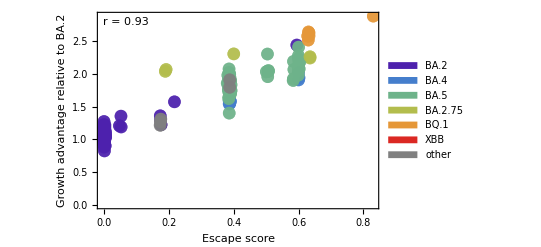

```mathematica
fig=ListPlot[Map[{#}&,escapeGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"Escape score","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[escapeGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/escape_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/escape_growth_advantage_correlation.png

```mathematica
bindingGAPairs=Table[{(pangoLineage/.pangoBindingMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
bindingGACorr=Correlation[bindingGAPairs[[All,1]],bindingGAPairs[[All,2]]]
```

0.859631

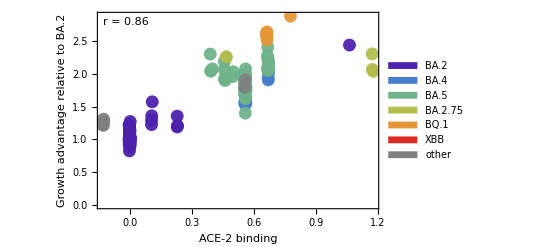

```mathematica
fig=ListPlot[Map[{#}&,bindingGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"ACE-2 binding","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[bindingGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/binding_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/binding_growth_advantage_correlation.png

```mathematica
bindingEscapePairs=Table[{(pangoLineage/.pangoBindingMapping)+RandomVariate[NormalDistribution[0,0.005]],(pangoLineage/.pangoEscapeMapping)+RandomVariate[NormalDistribution[0,0.005]]},{pangoLineage,pangoLineages}];
```

```mathematica
bindingEscapeCorr=Correlation[bindingEscapePairs[[All,1]],bindingEscapePairs[[All,2]]]
```

0.817069

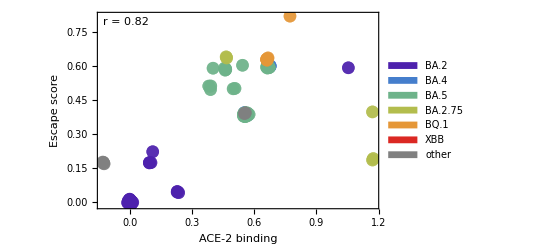

```mathematica
fig=ListPlot[Map[{#}&,bindingEscapePairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"ACE-2 binding","Escape score"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[bindingEscapeCorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/binding_escape_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/binding_escape_correlation.png

```mathematica
gaColors=Table[colorRamp[((pangoLineage/.pangoGAMapping)-0.5)/2],{pangoLineage,pangoLineages}]
```

{RGBColor[0.88926021006208, 0.73287944506864, 0.3805847966777601],RGBColor[0.911141696180572, 0.7856607869690635, 0.502977345739634],RGBColor[0.90823864125688, 0.77865819429079, 0.48673931280835997],RGBColor[0.8251571765096, 0.6764643542543, 0.30900033990119996],RGBColor[0.8227596822449599, 0.67589293124618, 0.31081863228312],RGBColor[0.8190400557415999, 0.6750063889103, 0.31363964780520004],RGBColor[0.70232330610608, 0.64718791311314, 0.40215922419576],RGBColor[0.89771552701216, 0.75327490506628, 0.42787901559152003],RGBColor[0.8347378562397199, 0.678747830345135, 0.30173422159434005],RGBColor[0.8889630231382, 0.732162586782475, 0.37892250258289994],RGBColor[0.8947405478942799, 0.7460988207218651, 0.41123867975366],RGBColor[0.8848162071879999, 0.7221598607665, 0.3557275800859999],RGBColor[0.8802113791386399, 0.71105234264137, 0.32997079922107997],RGBColor[0.88627237582192, 0.7256723522908599, 0.3638725566202399],RGBColor[0.90426048967024, 0.76906231136542, 0.46448780253127997],RGBColor[0.89554367058388, 0.748036070003665, 0.41573088986485995],RGBColor[0.88950217871824, 0.73346310882442, 0.38193823128728],RGBColor[0.89570757697576, 0.74843143617133, 0.41664768870572],RGBColor[0.8923131654568, 0.7402436195869, 0.39766128731960004],RGBColor[0.898951219550548, 0.7562555760316465, 0.43479077463800603],RGBColor[0.8753762050687599, 0.699389196255955, 0.30292559413921993],RGBColor[0.8983927640896, 0.7549084998568, 0.4316670934112],RGBColor[0.07335804273790404, 0.10250666200707209, 0.12279778961386412],RGBColor[0.89778338543356, 0.753438589494355, 0.42825857688482005],RGBColor[0.88453131646804, 0.721472662720945, 0.35413406394038005],RGBColor[0.8670223513475599, 0.686442573803855, 0.27724921974281996],RGBColor[0.89384269570828, 0.743933070052615, 0.40621660688666006],RGBColor[0.70704817366292, 0.648314046373235, 0.3985758201347399],RGBColor[0.8503957738055599, 0.682479766011605, 0.28985904314382005],RGBColor[0.8572901338529598, 0.68412297993518, 0.2846302663591201],RGBColor[0.8780697472955199, 0.70588641369466, 0.31799173257944],RGBColor[0.8636310856308798, 0.6856342935565399, 0.27982120196136007],RGBColor[0.8964113268471999, 0.7501289836951001, 0.4205840639684],RGBColor[0.77802858419264, 0.66523164250712, 0.34474330773407996],RGBColor[0.7596576714316399, 0.660853086784745, 0.35867605877958],RGBColor[0.8786023964926, 0.7071712413901751, 0.3209710682897],RGBColor[0.89139077818792, 0.7380186867126101, 0.39250197919724006],RGBColor[0.8819280610532799, 0.71519323026574, 0.3395729384141599],RGBColor[0.905578996712092, 0.7722427430142235, 0.471862778661074],RGBColor[0.8742843652181199, 0.696755518993585, 0.29681846495413994],RGBColor[0.8897044785020799, 0.73395108546364, 0.38306978085776],RGBColor[0.21876705130673602, 0.415414782764448, 0.552306488534376],RGBColor[0.21010508863230803, 0.398966659881144, 0.5304382128504781],RGBColor[0.149811670591712, 0.27436715742521595, 0.36107353806459197],RGBColor[0.12548947086111198, 0.21969316205441597, 0.285270852077492],RGBColor[0.5151669934620919, 0.600432444138056, 0.5428887594299221],RGBColor[0.8880309766135599, 0.729914354371855, 0.3737091660948201],RGBColor[0.89208977008768, 0.73970475731344, 0.39641174108096006],RGBColor[0.9200685649910401, 0.80757895783932, 0.5541623269588801],RGBColor[0.8202248134357999, 0.6752887661470249, 0.31274111139509997],RGBColor[0.49923854815417396, 0.596113863978932, 0.5546744319243091],RGBColor[0.519890603844206, 0.6017131271979079, 0.539393696109021],RGBColor[0.540831160415972, 0.6073906098638959, 0.523899494582502],RGBColor[0.5435269605151459, 0.6081215053528279, 0.521904835564311],RGBColor[0.259901127924524, 0.493523910260232, 0.6561549304280342],RGBColor[0.224472822707744, 0.42624942067219196, 0.566711466560304],RGBColor[0.505286798146478, 0.5977536883252039, 0.550199249808573],RGBColor[0.501006073673804, 0.596593082163272, 0.5533666158445141],RGBColor[0.5069998558425679, 0.5982181389878239, 0.5489317352093881],RGBColor[0.24970466139171202, 0.474161931825216, 0.6304125958645921],RGBColor[0.31690259782075403, 0.546678253523372, 0.6895872720063391],RGBColor[0.30654442503069795, 0.543869906655164, 0.6972514243943432],RGBColor[0.21517879386444205, 0.408601073035356, 0.5432474558506472],RGBColor[0.36781581547992803, 0.5604820370923039, 0.6519158924481481],RGBColor[0.275963705368094, 0.524024993853492, 0.6967070414140291],RGBColor[0.21504542267808807, 0.40834781569118406, 0.5429107425697082],RGBColor[0.20251919960428996, 0.3845618835502198, 0.511286628064515],RGBColor[0.26388652677887, 0.50109174823866, 0.666216599374545],RGBColor[0.26692997403135205, 0.506870922806736, 0.6739001863453321],RGBColor[0.276725670004184, 0.525471881636112, 0.6986307223798441],RGBColor[0.281589666800444, 0.534708081330792, 0.7109105285697541],RGBColor[0.29791297153837387, 0.5415297144345319, 0.7036379537790092],RGBColor[0.30194948372025787, 0.542624108839244, 0.7006512837258032],RGBColor[0.1577305299116961, 0.29216800120572817, 0.3857534935397363],RGBColor[0.297833680673942, 0.541508216796356, 0.7036966221638972],RGBColor[0.277519389684644, 0.526979068786392, 0.7006345731744541],RGBColor[0.20743115746756402, 0.39388915608295194, 0.5236875183406741],RGBColor[0.26926504915119803, 0.511304975914164, 0.6797953937460931],RGBColor[0.250173322046552, 0.475051867320336, 0.6315957919585321],RGBColor[0.34339512215001194, 0.5538610066246159, 0.6699850943136422],RGBColor[0.263826551980784, 0.500977862634912, 0.6660651850279441],RGBColor[0.290435075115416, 0.539502278956688, 0.7091709506587561],RGBColor[0.24534408372743005, 0.46588167018474, 0.6194037381625052],RGBColor[0.16979773293159203, 0.31929392769905607, 0.42336219716817214],RGBColor[0.23308288230965, 0.4425989852786999, 0.588448706041275],RGBColor[0.34329975881305996, 0.55383515135708, 0.6700556549387101],RGBColor[0.260216488365164, 0.4941227453597519, 0.6569510997622741],RGBColor[0.266236149776186, 0.5055534261795479, 0.6721485348249511],RGBColor[0.23754313639892002, 0.45106852158455996, 0.5997092101222201],RGBColor[0.12634155430987995, 0.22160856473383989, 0.28792645949857987],RGBColor[0.22437496085671998, 0.4260635916849599, 0.5664644013145199],RGBColor[0.26504018910512, 0.50328242723616, 0.6691291732039201],RGBColor[0.25641611348362997, 0.4869062477363399, 0.647356548419205],RGBColor[0.26269425782724803, 0.49882775946806396, 0.6632065579897681],RGBColor[0.246634120672802, 0.46833130971783593, 0.6226606078379071],RGBColor[0.253213953580814, 0.48082569514645196, 0.6392722702745491],RGBColor[0.08565089952204807, 0.13013983673446416, 0.16110976686156825],RGBColor[0.17054508305475202, 0.320973899807936, 0.42569139219723207],RGBColor[0.26497420744149797, 0.5031571352495638, 0.6689625937271431],RGBColor[0.267190521823976, 0.5073656746627679, 0.6745579738667161],RGBColor[0.4719046298884939, 0.588702988980692, 0.5748991683904291],RGBColor[0.360378635987354, 0.558465640942172, 0.6574187623194392],RGBColor[0.44789298098421193, 0.582192860180216, 0.5926657127433421],RGBColor[0.24451059984855203, 0.464298975156336, 0.6172994973655321],RGBColor[0.35570342160582796, 0.557198079188504, 0.6608780167837981],RGBColor[0.335205750943502, 0.551640673420436, 0.6760445210253571],RGBColor[0.36094831584667386, 0.5586200946939319, 0.6569972484730592],RGBColor[0.262642792755338, 0.4987300329066839, 0.663076627577583],RGBColor[0.385103188339412, 0.565169054813816, 0.6391247310465421],RGBColor[0.20709865243154, 0.39325776526571987, 0.52284806519739],RGBColor[0.34922201847911005, 0.55544081673098, 0.6656736947723851],RGBColor[0.2833497041880019, 0.537581266471436, 0.7144135126061072],RGBColor[0.2103280622295741, 0.39939006243613207, 0.5310011393232092],RGBColor[0.2351907602549, 0.44660161571819995, 0.59377032398715],RGBColor[0.20795000047823609, 0.39487438240144807, 0.5249974064596262],RGBColor[0.3095370301224079, 0.544681273032944, 0.6950371553408282],RGBColor[0.32542645503870793, 0.548989273836344, 0.6832803545628782],RGBColor[0.29235868220151795, 0.540023814563924, 0.7077476477132132],RGBColor[0.3879847147877059, 0.5659503051309079, 0.6369926505862712],RGBColor[0.25557984517229, 0.48531826537421996, 0.6452452779525151],RGBColor[0.4515308065560859, 0.5831791611677479, 0.5899740363146011],RGBColor[0.4117773316081459, 0.572401049126828, 0.6193881710398111],RGBColor[0.28152684499838, 0.53458878957684, 0.7107519265833301],RGBColor[0.666832796723, 0.638729042562125, 0.42907571104349995],RGBColor[0.180791178101774, 0.3433027392757319, 0.456431350785909],RGBColor[0.237358957141574, 0.45071878525213194, 0.5992442251152091],RGBColor[0.220786546985636, 0.41924958491464787, 0.557404973705526],RGBColor[0.25492603540160597, 0.48407675189110794, 0.6435946483149211],RGBColor[0.347673525043322, 0.555020983351196, 0.6668194460457271],RGBColor[0.32856130151221985, 0.5498392052339599, 0.6809608391837703],RGBColor[0.21859084991767996, 0.4150801955342398, 0.55186164471588],RGBColor[0.26624944622333596, 0.5055786746832479, 0.6721821034724761],RGBColor[0.33524468204360597, 0.551651228567108, 0.6760157153769211],RGBColor[0.39143806409165605, 0.5668865902170079, 0.634437470647596],RGBColor[0.268436195564504, 0.509731073305872, 0.677702842736964],RGBColor[0.3296628909204379, 0.550137872308484, 0.6801457582554332],RGBColor[0.258410799556436, 0.4906939391490479, 0.652392398443326],RGBColor[0.27190365869516003, 0.5163154078048799, 0.6864569141310601],RGBColor[0.15314594544720794, 0.2818622906793439, 0.37146515529762786],RGBColor[0.136029985735904, 0.24338723857107197, 0.318121472006864],RGBColor[0.36648930074794395, 0.560122387415792, 0.6528973986710042],RGBColor[0.31698885342327804, 0.546701639467604, 0.689523450317373],RGBColor[0.7814026455071599, 0.6660358222269049, 0.34218437356902004],RGBColor[0.8276449504401199, 0.677057294677085, 0.30711357818814],RGBColor[0.7466230776315198, 0.6577463987276599, 0.3685616726714401],RGBColor[0.273171232466288, 0.5187223922187839, 0.689657072538408],RGBColor[0.14229034204284804, 0.25745992506886406, 0.3376325289243682],RGBColor[0.05, 0.05, 0.05],RGBColor[0.05, 0.05, 0.05],RGBColor[0.05, 0.05, 0.05],RGBColor[0.05, 0.05, 0.05],RGBColor[0.05, 0.05, 0.05],RGBColor[0.05, 0.05, 0.05],RGBColor[0.31729485544175584, 0.5467846038888079, 0.6892970352779462],RGBColor[0.25938628949087605, 0.492546288196968, 0.6548551523958661]}

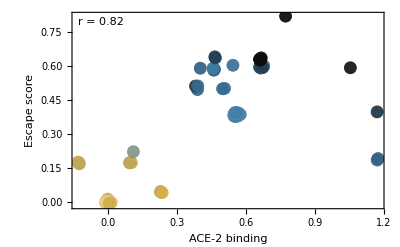

```mathematica
fig=ListPlot[Map[{#}&,bindingEscapePairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,gaColors],FrameLabel->{"ACE-2 binding","Escape score"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[bindingEscapeCorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->gaPanel]
```

```mathematica
Export["figures/binding_escape_correlation_ramp.png",fig,"PNG",ImageResolution->300]
```

figures/binding_escape_correlation_ramp.png

## Multiple regression

Predict continuous variable growth advantage Y from escape X_1 and binding X_2

```mathematica
regressionData=Table[{pangoLineage/.pangoEscapeMapping,pangoLineage/.pangoBindingMapping,pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
lm=LinearModelFit[regressionData,{x1,x2},{x1,x2}]
```

FittedModel[1.03004+1.45975 x1+0.447926 x2]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.03004 | 0.0208558 | 49.3886 | 1.64775×10^-95
x1 | 1.45975 | 0.0928675 | 15.7186 | 1.1288×10^-33
x2 | 0.447926 | 0.0688968 | 6.50141 | 1.08006×10^-9